Jonas Neundorf, Jan Skottke

# Blatt 6

```mathematica
transportMatrix[Ψ_] := {{√(β2/β1)(Cos[Ψ] + α1*Sin[Ψ]), √(β1*β2)Sin[Ψ]}, {((α1 - α2)Cos[Ψ] -(1+α1*α2)Sin[Ψ])/(√(β1*β2)), √(β2/β1)(Cos[Ψ] - α2*(Sin[Ψ]))}}
```

```mathematica
bmat={{β0,-α0},{-α0,γ0}}
```

{{β0,-α0},{-α0,γ0}}

Wir erfinden nun ein paar Parameter

```mathematica
params = {βp ->18.8, βk->10.6, αp->-1.0, αk->0.5, ϵ->3.0*10^-8, μ->23.27409747201 (* Phasenvorschub pro Umlauf*)};
```

definieren uns Ersetzungsregeln für β1 und β2 für die jeweiligen Abschnitte

```mathematica
leg1 = {α1->αp, α2->αk, β1->βp, β2->βk} (*pick-up -> kicker*)
```

{α1→αp,α2→αk,β1→βp,β2→βk}

```mathematica
leg2 = {α1->αk, α2->αp, β1->βk, β2->βp}(*kicker -> pick-up*)
```

{α1→αk,α2→αp,β1→βk,β2→βp}

sowie die Transportmatrizen für die Abschnitte

```mathematica
tmat1[Ψ_] := transportMatrix[Ψ] //.leg1;
tmat2[Ψ_]:= transportMatrix[Ψ] //.leg2
```

und legen willkürlich fest, dass der Phasenvorschub vom Pickup zum Kicker 5/2 π beträgt, also etwa ein Drittel des Umfangs

```mathematica
twissPickup = {α0->αp, β0->βp, γ0->γp}
```

{α0→αp,β0→βp,γ0→γp}

und prüfen, ob die Transportmatrix eigenltich stabil ist, d.h. der Betrag ihrer Spur kleiner als 2 ist.

```mathematica
Abs[Tr[tmat2[μ - n*π/2].tmat1[n*π/2] //.twissPickup //.γp->(1+αp^2)/βp//.n->5//.params]]
```

0.567778

Sie ist stabil. Nach einem vollen Umlauf sollten die Twiss-Parameter sich nicht geändert haben

```mathematica
{bmat //.twissPickup//.γp->(1+αp^2)/βp//.n->5//.params} =={tmat2[μ - n*π/2].tmat1[n*π/2].bmat.Transpose[tmat2[μ - n*π/2].tmat1[n*π/2]]//.twissPickup //.γp->(1+αp^2)/βp//.n->5//.params}
```

False

haben sie aber. Hmpf. Wir sehen aber den Fehler nicht und fahren fort in der Hoffnung, das alles irgendwie funktioniert.

Nun definieren wir eine Matrix für den Kicker.

```mathematica
kicker[g_] := {{1, 0}, {0, -g}} (*sollte so funktionieren*)
```

sowie für einen Umlauf inklusive Kicker.

```mathematica
kickedTransport[g_] := tmat2[μ - n*π/2].kicker[g].tmat1[n*π/2] //.γp->(1+αp^2)/βp//.n->5//. params
```

Nun erzeugen wir zufällig um die Sollbahn verteilte Teilchen und verfolgen sie für 100 Umläufe.

```mathematica
data = RandomVariate[d= MultinormalDistribution[{ 0, 0}, {{0.02, 0.01}, {0.01, 0.02}}], 10^3] ;
```

```mathematica
maxRevs = 60;
```

```mathematica
Manipulate[Histogram3D[Map[MatrixPower[kickedTransport[-.005], n].#&, data], AxesLabel->{"x_s", "x_s'", "Häufigkeit"}], {n, 0, maxRevs, 1}]
```

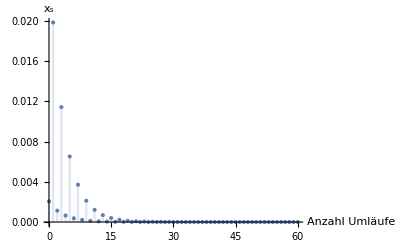

```mathematica
DiscretePlot[Mean[Map[(MatrixPower[kickedTransport[-.005], n].#)[[1]]&, data]], {n, 0, maxRevs}, AxesLabel->{"Anzahl Umläufe", "x_s"}, PlotRange->All]
```

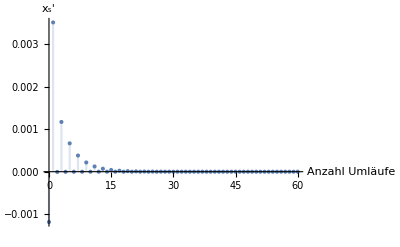

```mathematica
DiscretePlot[Mean[Map[(MatrixPower[kickedTransport[-.005], n].#)[[2]]&, data]], {n, 0, maxRevs}, AxesLabel->{"Anzahl Umläufe", "x_s'"}, PlotRange->All]
```

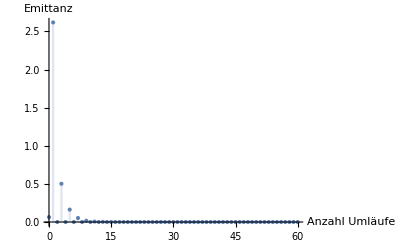

```mathematica
DiscretePlot[π*StandardDeviation[Map[(MatrixPower[kickedTransport[-.005], n].#)[[1]]&, data]]*StandardDeviation[Map[(MatrixPower[kickedTransport[-.005], n].#)[[2]]&, data]], {n, 0, maxRevs}, AxesLabel->{"Anzahl Umläufe", "Emittanz"}, PlotRange->All]
```

Wir vermuten, dass die Ausreißer durch den Fehler in der Transportmatrix entstehen.